```mathematica
k[T_]:=1/(n(k*T-b*n+((c/2)n^2)));
k[T]
```

1/(n (-b n+(c n^2)/2+k T))

```mathematica
k[T]/.n->(b/c)/.k->1/.b->1/.c->1
```

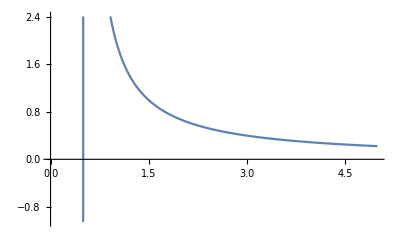

```mathematica
Plot[k[T]/.n->(b/c)/.k->1/.b->1/.c->1, {T,0,5}]
```